# Quantum Mechanics

## Path Integral Quantization

## From Classical to Quantum

### Historical Review

#### History: What is the Nature of Light?

There has been two theories in the history concerning the nature of light.

The corpuscular (particle) theory: light is composed of steady stream of particles carrying the energy and travelling along rays in the speed of light.

The wave theory: light is wave-like, propagating in the space and time.

The long-running dispute about this problem has lasted for centuries.

##### The Wave-Particle Wars in History

A time-line of “the wave-particle wars” in the history of physics. (c.f. Wikipedia, theories of light in history).

Ancient Greece | Pythagorean discipline postulated that every visible object emits a steady stream of particles, while Aristotle concluded that light travels in a manner similar to waves in the ocean.
Early 17th century	 | R. Descartes proposed light is a kind of pressure propagating in the media.
1662 | P. de Fermat stated the Fermat principle, the fundamental principle of geometric optics, where light rays are assumed to be trajectories of small particles.
1665 | P. Hooke expressly pointed out the wave theory of light in his book, where light was considered as some kind of fast pulses.
1672 | I. Newton conducted the dispersion experiment of light. He decomposed white light into seven colors. Thus he explained that light is a mixture of little corpuscles of different colors. His paper was strongly opposed by Hook, and “the first wave-particle war” broke out.
1675 | The phenomenon of Newton’s ring was discovered by Newton.
1690 | Dutch physicist C. Huygens considered light as longitudinal wave propagating in a media called ether. He introduced the concept of wave front, deduced the law of reflection and refraction, and explained the phenomenon of Newton’s ring. The wave theory reached its crest.
1704 | I. Newton published his book Optiks, which explained dispersion, double refraction, Newton’s ring and diffraction from particle viewpoint. On the other side, Newton integrated the corpuscular theory with his classical mechanics, which combined to show enormous strength over the century.
Early 18th century | “The first wave-particle war” ends, and corpuscular theory occupied the mainstream of physics for the following hundred years.
1807 | T. Young conducted the double-split experiment, and proposed light to be a longitudinal wave, which simply explained the interference and diffraction of light. Young’s experiment triggered “the second wave-particle war”. The corpuscular theory could do nothing but to suffer one defeat after another.
1809 | E. Malus discover the polarization of light, which could not be explained by longitudinal wave theory. This gave the wave theory a heavy strike.
1819 | A. Fresnel submitted a paper, perfectly explained the diffraction of light from wave viewpoint based on rigorous mathematical deductions. When Poisson applied this theory to circular disk diffraction, he predicted that a light spot will appear at the center of the shadow of the disk. This unreasonable effect was considered by Poisson as an opposing evidence of the wave theory. However, F. Arago insisted on doing the experiment and proved the existence of the Poisson spot. The success of Fresnel’s theory won the decisive battle for the wave in “the second wave-particle war”.
1821 | Fresnel proposed that light is a transverse wave, and successfully explained the polarization of light. “The second wave-particle war” ended with the victory of wave theory.
1865 | J. Maxwell formulated the classical theory of electrodynamics, which predicted that light is kind of electromagnetic wave.
1887 | H. R. Hertz verified the existence of electromagnetic wave in experiments. The speed of the electromagnetic wave is exactly the speed of light. The wave theory of light was firmly established.
1900 | M. Planck obtained the formula of blackbody radiation, the quantum hypothesis of light was proposed.
1905 | A. Einstein explained the photoelectric effect. In Einstein’s theory light is consisted of some particles carrying the discrete amount of energy, and can only be absorbed or emitted one by one. The concept of light quantum (photon) resurrected the particle theory. “The third wave-particle war” broke out.
1923 | A. Compton studied the scattering of X-ray by a free electron. The Compton effect was discovered, that the frequency of X-ray changes in the scattering. The experiment exactly proved that X-ray is also composed by radiation quantum with certain momentum and energy.
1924 | S. N. Bose considered light as a set of indistinguishable particles and obtained Planck’s formula of blackbody radiation. Bose-Einstein statistics was established, which further supports the idea of particle theory.
… | …

##### Concluding Remarks

In fact, “the third wave-particle war” had gone beyond the scope of the nature of light. The discussion had been extended to the nature of all matter in general.

Light: originally considered as wave, also behaves like particle.

Electrons, α particles (^4He nucleus): originally considered as particles, also behave like wave.

The dispute ends up with the discovery of wave-particle duality, which finally leads to the formulation of quantum mechanics. Another century has passed, we hope that wave and particle will live in peace under the quantum framework, and there should be no more wars.

### Quantization of Light

#### Geometric Optics

Geometric optics is the particle mechanics of light (light travels along a path)

Its basic principle is Fermat’s Principle

Light always travels along the path of extremal optical path length.

δL=0,

The optical path length is defined by

L(A→B)=∫_A^B nⅆs,

where n is the refractive index of the medium and ⅆs is an infinitesimal displacement along the ray.

The optical path length is simply related to the light travelling time T by L=c T, where c is the speed of light in vacuum. So extremization of either of them will be equivalent.

Eikonal equation (Newton’s law of light)

nⅆ/ⅆt(n^2 ⅆx/ⅆt)=∇n.

It can be derived from Fermat’s principle.

Refraction (Snell’s law)

```mathematica
Module[{x0=-1,y0=-1,θ=30Degree,n,tend=5,sol,data,xmin,xmax,ymin,ymax,colbg=ColorData["Legacy"]["DodgerBlue"],colray=ColorData["Legacy"]["Firebrick"]},n[x_,y_]:=1.366+0.366Tanh[25y];sol=NDSolve[{n[x[t],y[t]]D[n[x[t],y[t]]^2D[x[t],t],t]==D[n[x[t],y[t]],x[t]],n[x[t],y[t]]D[n[x[t],y[t]]^2D[y[t],t],t]==D[n[x[t],y[t]],y[t]],x[0]==x0,y[0]==y0,x'[0]==Cos[θ]/n[x0,y0],y'[0]==Sin[θ]/n[x0,y0]},{x,y},{t,0,tend}];data=First@Cases[ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,tend},PlotPoints->10,MaxRecursion->3],Line[pts_]:>pts,∞];{{xmin,xmax},{ymin,ymax}}={Min[#],Max[#]}&/@Thread[data];Show[ContourPlot[n[x,y],{x,xmin,xmax},{y,ymin,ymax},Contours->16,ContourStyle->None,ColorFunction->(Blend[{White,colbg},Rescale[#,{0.9,2.0}]]&),ColorFunctionScaling->False],Graphics[{AbsoluteThickness[1.2],colray,Arrowheads[{{0.001,0.2,Arrowhead[]},{0.001,0.8,Arrowhead[]}}],Arrow[data]}],AspectRatio->Automatic,PlotRangePadding->0.05,FrameTicks->None,ImageSize->120]]
```

-Graphics-

Total reflection

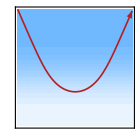

```mathematica
Module[{x0=-1,y0=1,θ=-45Degree,n,tend=6.6,sol,data,xmin,xmax,ymin,ymax,colbg=ColorData["Legacy"]["DodgerBlue"],colray=ColorData["Legacy"]["Firebrick"]},n[x_,y_]:=1.3+0.3Tanh[3y];sol=NDSolve[{n[x[t],y[t]]D[n[x[t],y[t]]^2D[x[t],t],t]==D[n[x[t],y[t]],x[t]],n[x[t],y[t]]D[n[x[t],y[t]]^2D[y[t],t],t]==D[n[x[t],y[t]],y[t]],x[0]==x0,y[0]==y0,x'[0]==Cos[θ]/n[x0,y0],y'[0]==Sin[θ]/n[x0,y0]},{x,y},{t,0,tend}];data=First@Cases[ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,tend},PlotPoints->10,MaxRecursion->3],Line[pts_]:>pts,∞];{{xmin,xmax},{ymin,ymax}}={Min[#],Max[#]}&/@Thread[data];Show[ContourPlot[n[x,y],{x,xmin,xmax},{y,ymin-0.5,ymax},Contours->16,ContourStyle->None,ColorFunction->(Blend[{White,colbg},Rescale[#,{0.9,2.0}]]&),ColorFunctionScaling->False],Graphics[{AbsoluteThickness[1.2],colray,Arrowheads[{{0.001,0.2,Arrowhead[]},{0.001,0.8,Arrowhead[]}}],Arrow[data]}],AspectRatio->Automatic,PlotRangePadding->0.05,FrameTicks->None,ImageSize->140]]
```

Gradient-index (GRIN) optics

```mathematica
Module[{x0=-5,θ=0Degree,n,tend=13,sols,datas,colbg=ColorData["Legacy"]["DodgerBlue"],colray=ColorData["Legacy"]["Firebrick"]},n[x_,y_]:=1+0.8Exp[-((x/2)^10+y^2/14)];sols=NDSolve[{n[x[t],y[t]]D[n[x[t],y[t]]^2D[x[t],t],t]==D[n[x[t],y[t]],x[t]],n[x[t],y[t]]D[n[x[t],y[t]]^2D[y[t],t],t]==D[n[x[t],y[t]],y[t]],x[0]==x0,y[0]==#,x'[0]==Cos[θ]/n[x0,#],y'[0]==Sin[θ]/n[x0,#]},{x,y},{t,0,tend}]&/@{-2,-1,0,1,2};datas=Cases[ParametricPlot[Evaluate[{x[t],y[t]}/.sols],{t,0,tend},PlotPoints->10,MaxRecursion->3],Line[pts_]:>pts,∞];
Show[ContourPlot[n[x,y],{x,-5,5},{y,-5,5},Contours->16,ContourStyle->None,PlotRange->All,ColorFunction->(Blend[{White,colbg},Rescale[#,{0.9,2.0}]]&),ColorFunctionScaling->False],Graphics[{AbsoluteThickness[1.2],colray,Arrowheads[{{0.001,0.2,Arrowhead[]},{0.001,0.6,Arrowhead[]}}],Arrow/@datas}],AspectRatio->Automatic,PlotRangePadding->0.2,FrameTicks->None,ImageSize->120]]
```

-Graphics-

#### Physical Optics

Physical optics is the wave mechanics of light (light propagates in the spacetime as a wave)

Its basic principle is Huygens’ Principle

Every point on the wavefront is a source of spherical wavelet. Wavelets from the past wavefront interferes to determine the new wavefront.

ψ=ψ_0 e^(ⅈ Θ).

The new wave amplitude ψ receives contribution from the previous one ψ_0 with additional phase factor e^(ⅈ Θ).

Interference effect: contributions from different paths must be collected and summed up

ψ_B=∫_(A→B) ψ_A e^(ⅈ Θ(A→B)).

The accumulated phase Θ is determined by the propagation time × the frequency of light

Θ=ω T=ω/c L.

The phase is proportional to the optical path length (given that the light propagates with a fixed frequency).

What about the amplitude of the wave? It is related to the intensity of the light, or the probability density to observe a photon,

p(x)=(|ψ(x)|)^2.

#### From Fermat to Huygens

Optimizing the optical path length L can be viewed as optimizing an action S=(ℏ ω/c)L  (which is defined by properly rescaling L to match the dimension of energy × time).

Particle mechanics defines the action S in the variational principle δS=0.

Wave mechanics defines the phase Θ in the wavelet propagator e^(ⅈ Θ).

They are related by

S=ℏ Θ.

The Planck constant ℏ provides a natural unit for the action.

Therefore the particle and wave mechanics are connected by

The action accumulated by particle = the phase accumulated by wave.

This is also the guiding principle of the path integral quantization (a procedure to promote classical theory to its quantum version).

## Path Integral Quantization

### Quantization of Matter

#### Classical Mechanics

Action: a function(al) associated to each possible path of a particle,

S[x]=∫L(x,ẋ,t)ⅆt.

The principle of stationary action: the path taken by the particle x̄(t) is the one for which the action is stationary (to first order), subject to boundary conditions: x̄(t_0)=x_0 (initial) and x̄(t_1)=x_1 (final).

((δ S[x]|)_(x=x̄)=δ∫L(x,ẋ,t)ⅆt|)_(x=x̄)=0.

This leads to the Euler-Lagrange equation (the equation of motion),

ⅆ/ⅆt((∂L)/(∂ẋ))-(∂L)/(∂x)=0,

such that the classical path x̄(t) is the solution of Eq. (DisplayFormulaNumbered). For a non-relativistic particle, the Lagrangian takes the form of L=T-V, where T is the kinetic energy and V is the potential energy. For a relativistic particle, the action is simply the proper time of the path in the spacetime.

For a non-relativistic free particle L=(m/2) (ẋ)^2.
(i) Show that the stationary (classical) action S[x̄] corresponding to the classical motion of a free particle travelling from (x_0,t_0) to (x_1,t_1) is S[x̄]=m/2(x_1-x_0)^2/(t_1-t_0).
For this case of the free particle,
(ii) Show that the spatial derivative of the action ∂_x_1 S[x̄] is the momentum of the particle.
(iii) Show that the (negative) temporal derivative of the action -∂_t_1 S[x̄] is the energy of the particle.

A computability problem: the principle of stationary action is formulated as a deterministic global optimization, which requires exact computations and indefinitely long run time (on any computer).

Nature may not have sufficient computational resources to carry out the classical mechanics precisely. ⇒ Classical mechanics might actually be realized only approximately as a stochastic global optimization, which is computationally more feasible.

Quantum mechanics takes a stochastic approach to optimize the action, which is more natural than the deterministic approach of classical mechanics, if we assume only limited computational resource is available to nature.

#### Optimization by Interference

Each path is associated with an action. Quantum mechanics effectively finds the stationary action by the interference among all possible paths.

Example: find the stationary point(s) of

f(x)=-x^2+2x^4.

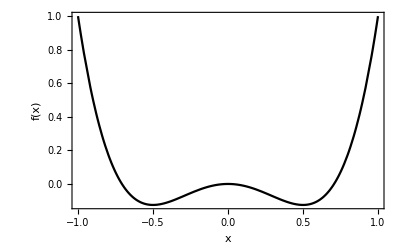

```mathematica
Plot[-x^2+2x^4,{x,-1,1},PlotStyle->Black,FrameLabel->{"\!\(x\)","\!\(f(x)\)"}]
```

Every point x is a legitimate guess of the solution.

Each point x is associated with an action f(x) (the objective function).

Raise the action f(x) to the exponent (as a phase): e^(ⅈ f(x)/ℏ) ⇒ call it a “probability amplitude” contributed by the point x.

A “Planck constant” ℏ=h/(2π) is introduced as a hyperparameter of the algorithm, to control “how quantum” the algorithm will be.

Contributions from all points must be collected and summed (integrated) up,

Z=∫_(-∞)^∞ e^(ⅈ f(x)/ℏ)ⅆx.

The result Z summarizes the probability amplitudes. It is known as the partition function of the stationary problem. But it is just a complex number, how do we make use of it? ⇒ Well, we need to analyze how Z is accumulated. Each infinitesimal step in the integral → a infinitesimal displacement on the complex plane

ⅆz=e^(ⅈ f(x)/ℏ)ⅆx.

ⅆx controls the infinitesimal step size,

e^(ⅈ f(x)/ℏ) controls the direction to make the displacement,

displacement ⅆz is accumulated to form the partition function,

Z≡∫ⅆz.

Let us see how the partition function is constructed.

For small h (classical limit)

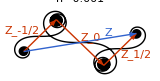

```mathematica
Block[{f,h=0.001,dx,acc,Z1,Z2},
f[x_]:=-x^2+2x^4;
dx=0.01Sqrt[h];
acc=ReIm@Prepend[Accumulate[Table[Exp[2π ⅈ f[x]/h]dx,{x,dx/2,1/2+2Sqrt[2h],dx}]],0];
{Z1,Z2}={NIntegrate[Exp[2π ⅈ f[x]/h],{x,0,1/(2Sqrt[3])}],NIntegrate[Exp[2π ⅈ f[x]/h],{x,1/(2Sqrt[3]),∞}]};
Graphics[{{AbsoluteThickness[1],Line/@{acc,-acc}},{Arrowheads[0.08],
{Red,Arrow/@ReIm/@{{-Z1-Z2,-Z1},{-Z1,Z1},{Z1,Z1+Z2}},Text["\!\(Z\_\("<>#1<>"\)\)",ReIm@#2,#3]&@@@{{"-1/2",-Z1-Z2/2,{1,-1}},{"0",0,{-0.5,-1}},{"1/2",Z1+Z2/2,{-1,1}}}},
{Blue,Arrow/@ReIm/@{{-Z1-Z2,Z1+Z2}},
Text["\!\(Z\)",ReIm@(Z1+Z2)/2,{0,-0.6}]}}},
PlotLabel->Style["\!\(h="<>ToString[h]<>"\)",14,Black],ImageSize->160]
]
```

Z=Z_(-1/2)+Z_0+Z_(1/2),

Z can break up into three smaller contributions, which correspond to the contributions around the three stationary points: x=0,±1/2.

Around the stationary point, phase changes slowly ∂_x f(x)∼0 ⇒ constructive interference ⇒ large contribution to the partition function.

The solutions of stationary points (classical solutions) emerge from interference due to their dominant contribution to the probability amplitude.

*More precisely, the partition function is actually evaluated with respect to the momentum k,

Z(k)≡∫ⅆz e^(ⅈ k x)≃Z_(-1/2)e^(-ⅈ k/2)+Z_0+Z_(1/2)e^(ⅈ k/2).

Then its Fourier spectrum Z̃(x)=∫ⅆk Z(k)e^(-ⅈ k x) will reveal the saddle points.

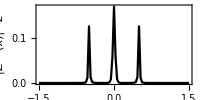

```mathematica
Block[{ϵ=0.0001,ℏ=0.001,a=1/32,L=3,Z},
Z[k_]:=NIntegrate[Exp[(ⅈ-ϵ)(-x^2+2x^4)/ℏ]Exp[ⅈ k x],{x,-∞,∞}];
ListLinePlot[RotateLeft[#,Ceiling[Length[#]/2]]&[Abs[Fourier[Z/@Range[-π/a,π/a,2π/L]]]^2],DataRange->{-L/2,L/2},FrameLabel->{"\!\(x\)","\!\(|Z\&~(x)|\^2\)"},PlotStyle->Black,PlotRange->All,AspectRatio->1/2,ImageSize->200]]
```

For intermediate h

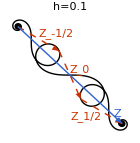

```mathematica
Block[{f,h=0.1,dx,acc,Z1,Z2},
f[x_]:=-x^2+2x^4;
dx=0.01Sqrt[h];
acc=ReIm@Prepend[Accumulate[Table[Exp[2π ⅈ f[x]/h]dx,{x,dx/2,1/2+Sqrt[2h],dx}]],0];
{Z1,Z2}={NIntegrate[Exp[2π ⅈ f[x]/h],{x,0,1/(2Sqrt[3])}],NIntegrate[Exp[2π ⅈ f[x]/h],{x,1/(2Sqrt[3]),∞}]};
Graphics[{{AbsoluteThickness[1],Line/@{acc,-acc}},{Arrowheads[0.08],
{Red,Dashed,Arrow/@ReIm/@{{-Z1-Z2,-Z1},{-Z1,Z1},{Z1,Z1+Z2}},Text["\!\(Z\_\("<>#1<>"\)\)",ReIm@#2,#3]&@@@{{"-1/2",-Z1-Z2/2,{-1,-1}},{"0",0,{-1,-1}},{"1/2",Z1+Z2/2,{1,1}}}},
{Blue,Arrow/@ReIm/@{{-Z1-Z2,Z1+Z2}},Text["\!\(Z\)",0.9ReIm@(Z1+Z2),{0,-1}]}}},
PlotLabel->Style["\!\(h="<>ToString[h]<>"\)",14,Black],ImageSize->140]
]
```

The decomposition of Z into three subdominant amplitudes is not very well defined. ⇒ Quantum fluctuations start to smear out nearby stationary points.

For large h (quantum limit)

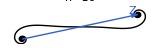

```mathematica
Block[{f,h=10,dx,acc,Z1,Z2},
f[x_]:=-x^2+2x^4;
dx=0.01Sqrt[h];
acc=ReIm@Prepend[Accumulate[Table[Exp[2π ⅈ f[x]/h]dx,{x,dx/2,1/2+Sqrt[h/2],dx}]],0];
{Z1,Z2}={NIntegrate[Exp[2π ⅈ f[x]/h],{x,0,1/(2Sqrt[3])}],NIntegrate[Exp[2π ⅈ f[x]/h],{x,1/(2Sqrt[3]),∞}]};
Graphics[{{AbsoluteThickness[1],Line/@{acc,-acc}},{Arrowheads[0.08],
{Blue,Arrow/@ReIm/@{{-Z1-Z2,Z1+Z2}},Text["\!\(Z\)",0.9ReIm@(Z1+Z2),{0,-1}]}}},
PlotLabel->Style["\!\(h="<>ToString[h]<>"\)",14,Black],ImageSize->160]
]
```

Stationary points are indistinguishable if quantum fluctuations are too large. ⇒ As if there is only one (approximate) stationary point around x=0.

If there is no sufficient resolution power, fine structures in the action landscape will be ignored by quantum mechanics. In this way, the computational complexity is controlled.

Generalize the same problem from stationary points to stationary paths (in classical mechanics) ⇒ path integral formulation of quantum mechanics.

The Planck constant characterizes nature’s resolution (computational precision) of the action.

h=6.62607004×10^-34 J s.

Two nearby paths with an action difference smaller than the Planck constant can not be resolved.

h is very small (in our everyday unit) ⇒ our nature has a pretty high resolution of action ⇒ no need to worry about the resolution limit in the macroscopic world ⇒ classical mechanics works well.

However, in the microscopic world, nature’s resolution limit can be approached ⇒ “round-off error” may occur ⇒ one consequence is the quantization of atomic orbitals (discrete energy levels etc.).

#### Path Integral and Wave Function

Feynman’s principles:

The probability p_(A→B) for a particle to propagate from A to B is given by the square modulus of a complex number K_(A→B) called the transition amplitude

p_(A→B)=(|K_(A→B)|)^2.

The transition amplitude is given by adding together the contributions of all paths x from A to B.

```mathematica
Block[{randpath},
randpath[p1_,p2_]:=BSplineCurve@Table[(1-t)p1+t p2+{0,t(1-t)RandomReal[{-1,1}]},{t,0,1,0.05}];
Graphics[{{Opacity[0.5],AbsoluteThickness[1],Table[{ColorData[0,i],randpath[{0,0},{1,0}]},{i,10}]},Point/@{{0,0},{1,0}},
Text["\!\(A\)",{0,0},{1.2,0}],Text["\!\(B\)",{1,0},{-1.2,0}]}]]
```

-Graphics-

K_(A→B)∝∫_(A→B) ⅅ[x]e^(ⅈ S[x]/ℏ).

The contribution of each particular path is proportional to e^(ⅈ S[x]/ℏ), where S[x] is the action of the path x.

In the limit of ℏ→0, the classical path x̄ (that satisfies δS[x̄]=0) will dominate the transition amplitude,

K_(A→B)∼e^(ⅈ S[x̄]/ℏ).

Quantum mechanics reduces to classical mechanics in the limit of ℏ→0.

To make the problem tractable, an important observation is that the transition amplitude satisfies a composition property

K_(A→B)=∫_C K_(A→C)K_(C→B).

This allows us the chop up time into slices t_0<t_1<…<t_(N-1)<t_N,

K_((x_0,t_0)→(x_N,t_N))=∫ⅆ x_1…ⅆ x_(N-1)K_((x_0,t_0)→(x_1,t_1))… K_((x_(N-1),t_(N-1))→(x_N,t_N)).

The “front” of transition amplitude propagates in the form of wave ⇒ define the wave function ψ(x,t), which describes the probability amplitude to observe the particle at (x,t),

ψ(x_(k+1),t_(k+1))=∫ⅆ x_k K_((x_k,t_k)→(x_(k+1),t_(k+1)))ψ(x_k,t_k).

If we start with a initial wave function ψ(x,t_0) concentrated at x_0, following the time evolution Eq. (DisplayFormulaNumbered), the final wave function ψ(x,t_N) will give the transition amplitude K_((x_0,t_0)→(x_N,t_N))=ψ(x_N,t_N). ⇒ It is sufficient to study the evolution of a generic wave function over one time step, then the dynamical rule can be applied iteratively.

Putting together Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered),

ψ(x_(k+1),t_(k+1))∝∫ⅅ[x]exp(ⅈ/ℏ S[x])ψ(x_k,t_k),

this path integral involves multiple integrals:

for each given initial point x_k, integrate over paths x(t) subject to the boundary conditions x(t_k)=x_k and x(t_(k+1))=x_(k+1),

finally integrate over choices of initial point x_k.

The Schrödinger equation is the equation that governs the time evolution of the wave function, which plays a central role in quantum mechanics. It can be derived from the path integral formulation in Eq. (DisplayFormulaNumbered).

### Deriving the Schrödinger Equation

#### Action in a Time Slice

The action of a free particle of mass m,

S[x]=∫_t_0^t_1 ⅆt 1/2 m (ẋ)^2,

where the particle starts from x(t_0)=x_0, ends up at x(t_1)=x_1.

Suppose the time interval δt=t_1-t_0 is small, approximate the path of the particle by a straight line in the space-time,

x(t)=x_0+v t,

where the velocity v will be a constant

v=(x_1-x_0)/(t_1-t_0)=(x_1-x_0)/δt.

Plug into Eq. (DisplayFormulaNumbered), we get an estimate of the action accumulated as the particle moves from x_0 to x_1 in time δt,

S[x]=1/2(m((x_1-x_0)/δt))^2 δt=m/(2δt)(x_1-x_0)^2.

#### Path Integral in a Time Slice

The wave function ψ(x,t+δt) in the next time slice is related to the previous one ψ(x,t) by

ψ(x_1,t+δt)∝∫ⅆ x_0exp(ⅈ/ℏ S[x])ψ(x_0,t)
=∫ⅆ x_0exp((ⅈ m)/(2ℏ δt)(x_1-x_0)^2)ψ(x_0,t).

The proportional sign “∝” implies that the normalization factor is not determined yet. (It will be determined later.)

To proceed we expand ψ(x_0,t) around x_0→x_1, by defining x_0=x_1+a, and Taylor expand with respect to a,

ψ(x_0,t)=ψ(x_1+a,t)
=ψ(x_1,t)+a ψ'(x_1,t)+a^2/(2!)ψ''(x_1,t)+a^3/(3!)ψ^(3)(x_1,t)+…
=∑_(n=0)^∞ a^n/(n!)∂_x_1^n ψ(x_1,t).

Substitute into Eq. (DisplayFormulaNumbered),

ψ(x_1,t+δt)∝∑_(n=0)^∞ ∫ⅆa exp((ⅈ m)/(2ℏ δt)a^2)a^n/(n!)∂_x_1^n ψ(x_1,t).

We pack everything related to the integral of a into a coefficient

λ_n≡∫ⅆa exp((ⅈ m)/(2ℏ δt)a^2)a^n/(n!),

then the time evolution is simply given by (we are free to replace x_1 by x)

ψ(x,t+δt)∝∑_(n=0)^∞ λ_n∂_x^n ψ(x,t).

The idea is that the time-evolved wave function can be expressed as the original wave function “dressed” by its (different orders of) derivatives.

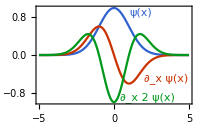

```mathematica
Plot[{Exp[-x^2/2],-x Exp[-x^2/2],(x^2-1)Exp[-x^2/2]},{x,-5,5},PlotRange->All,Epilog->{{#1,Text["\!\("<>#2<>" ψ(x)\)",#3]}&@@@{{Blue,"",{1.8,0.9}},{Red,"∂\_x",{3.5,-0.5}},{Green,"∂\_x\%2",{2.2,-0.9}}}},FrameLabel->{"\!\(x\)","\!\(∂\_x\%n ψ(x)\)"},ImageSize->200]
```

For example, ψ(x) is a wave packet.

ψ(x)+λ ψ'(x): shift the wave packet around.

ψ(x)+λ ψ''(x): expand or shrink the wave packet.

Locality of Physics: the time evolution should only involve local modifications of the wave function ψ(x) (within the light-cone) in each step.

#### Computing the Coefficients λ_n

The λ_n coefficient can be computed by Mathematica

λ_n=(1+(-1)^n)/2(√π)/(2^n Γ(1+n/2))(-(ⅈ m)/(2ℏ δt))^(-(1+n)/2).

```mathematica
FunctionExpand[Integrate[Exp[ⅈ c a^2]a^n/n!,{a,-∞,∞}, GenerateConditions->False]]
```

(2^(-1-n) (1+(-1)^n) (-ⅈ c)^(-1/2-n/2) √π)/Gamma[1+n/2]

Evaluate the integral for λ_n.

The first term (1+(-1)^n)/2 just discriminates even and odd n.

(1+(-1)^n)/2=Piecewise[{{1, if n∈even,}, {0, if n∈odd.}}]

So as long as n∈odd, λ_n=0. We only need to consider the case of even n.

For even n, the first several λ_n are given by

λ_0=√π(-(ⅈ m)/(2ℏ δt))^(-1/2),
λ_2=(√π)/4(-(ⅈ m)/(2ℏ δt))^(-3/2)=ⅈ/4((2ℏ δt)/m)λ_0,
λ_4=(√π)/32(-(ⅈ m)/(2ℏ δt))^(-5/2)=-1/32((2ℏ δt)/m)^2 λ_0,
…

```mathematica
Block[{λ},
λ=Association@Table[
n->Sqrt[π]/(2^n Gamma[1+n/2])(-ⅈ c)^(-(1+n)/2),{n,0,4,2}];
{λ,λ/λ[0]}]
```

{<|0→(√π)/(√(-ⅈ c)),2→(√π)/(4 (-ⅈ c)^(3/2)),4→(√π)/(32 (-ⅈ c)^(5/2))|>,<|0→1,2→ⅈ/(4 c),4→-1/(32 c^2)|>}

The first several λ_n for even n.

#### Determining the Normalization

Plugging the results of λ_n in Eq. (DisplayFormulaNumbered) into Eq. (DisplayFormulaNumbered), we get

ψ(x,t+δt)∝λ_0(1+ⅈ/4((2ℏ δt)/m)∂_x^2 -1/32((2ℏ δt)/m)^2∂_x^4 +…)ψ(x,t).

If we take δt=0, all higher order terms vanishes,

ψ(x,t)∝λ_0 ψ(x,t).

So obviously, the normalization factor should be such to cancelled out λ_0.

So we should actually write (in equal sign) that

ψ(x,t+δt)=(1+ⅈ/4((2ℏ δt)/m)∂_x^2 -1/32((2ℏ δt)/m)^2∂_x^4 +…)ψ(x,t).

#### Taking the Limit of δt→0

Let us consider the time derivative of the wave function

∂_t ψ(x,t)=lim_(δt→0) (ψ(x,t+δt)-ψ(x,t))/δt
=lim_(δt→0) 1/δt(ⅈ/4((2ℏ δt)/m)∂_x^2 -1/32((2ℏ δt)/m)^2∂_x^4 +…)ψ(x,t)

Only the first term survives under the limit δt→0,

∂_t ψ(x,t)=(ⅈ ℏ)/(2m)∂_x^2 ψ(x,t).

All the higher order terms will have higher powers in δt, so they should all vanish under the limit δt→0.

By convention, we write Eq. (DisplayFormulaNumbered) in the following form

ⅈ ℏ∂_t ψ(x,t)=-ℏ^2/(2m)∂_x^2 ψ(x,t).

This is the Schrödinger equation that governs the time evolution of the wave function of a free particle.

#### Adding Potential Energy

Now suppose the particle is not free but moving in a potential V(x), the action changes to

S=∫_t_0^t_1 ⅆt (1/2 m (ẋ)^2-V(x)),

The additional action that will be accumulated over time δt will be

ΔS=-V(x)δt.

Eventually this cause an additional phase shift in the wave function

ψ(x,t+δt)=e^(ⅈ ΔS/ℏ)ψ_0(x,t+δt)
=e^(-ⅈ V(x)δt/ℏ)ψ_0(x,t+δt)
=(1-ⅈ/ℏ V(x)δt+…)ψ_0(x,t+δt),

where ψ_0 is the expected wave function at t+δt without the potential. Combining with the result in Eq. (DisplayFormulaNumbered), to the first order of δt we have

ψ(x,t+δt)=(1-ⅈ/ℏ V(x)δt+…)(1+ⅈ/4((2ℏ δt)/m)∂_x^2 +…)ψ(x,t)
=(1+ⅈ/4((2ℏ δt)/m)∂_x^2 -ⅈ/ℏV(x)δt+…)ψ(x,t).

Then after taking the δt→0 limit, we arrive at

∂_t ψ(x,t)=(ⅈ ℏ)/(2m)∂_x^2 ψ(x,t)-ⅈ/ℏ V(x)ψ(x,t),

or equivalently written as

ⅈ ℏ∂_t ψ(x,t)=-ℏ^2/(2m)∂_x^2 ψ(x,t)+V(x)ψ(x,t).

This is the Schrödinger equation that governs the time evolution of the wave function of a particle moving in a potential V(x).

## Single-Particle Quantum Mechanics

### Wave Mechanics v.s. Matrix Mechanics

#### Functions as Vectors

To specify a function ψ is to specify the values ψ(x) of the function at each point x ⇒ these values can be arranged into an infinite-dimensional vector

ψ(x)∼(⋯ | ψ(0) | ⋯ | ψ(0.01) | ⋯ | ψ(0.5) | ⋯)ᵀ.

Elements of the vector are labeled by real numbers x∈ℝ (instead of integers). The vector is like a look-up table representation of the function.

Quantum states of particles are represented by state vectors wave functions.

The ket state:

ψ≏ψ(x).

ψ:ℝ→ℂ is a complex function in general.

The bra state:

ψ≏ψ^*(x).

Inner product of bra and ket

ϕψ=∫ⅆx ϕ^*(x)ψ(x),

as a functional generalization of ϕψ=∑_i ϕ_i^*ψ_i.

Normalized state: ψ is normalized iff

ψψ=∫ⅆx ψ^*(x)ψ(x)=∫ⅆx (|ψ(x)|)^2=1.

Orthogonal states: two states ϕ and ψ are orthogonal iff

ϕψ=∫ⅆx ϕ^*(x)ψ(x)=0.

Can we find a complete set of orthonormal basis?

Dirac δ-function: a infinitely sharp peak of unit area.

It can be considered as the limit of Gaussians with σ→0

δ(x)=lim_(σ→0) 1/(√(2π)σ)e^(-x^2/(2 σ^2)).

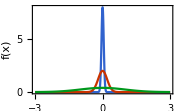

```mathematica
Block[{σs={0.05,0.2,1.},sty=Style[#,FontFamily->"CMU"]&},
Plot[Evaluate@Table[Exp[-x^2/(2σ^2)]/(Sqrt[2π]σ),{σ,σs}],{x,-3,3},PlotRange->All,FrameLabel->{"\!\(x\)","\!\(f(x)\)"},PlotLegends->LineLegend[Automatic,sty/@σs,LegendLabel->sty@"\!\(σ=\)",LegendMargins->1],ImageSize->180]]
```

Loosely speaking

δ(x)=Piecewise[{{0, if x≠0,}, {∞, if x=0  (ill–defined).}}]

The area under the curve remains unity as the limit is taken, i.e. ∫δ(x)ⅆx=1, as a functional generalization of ∑_i δ_ij=1.

Multiplying δ(x-a) with an ordinary function ψ(x) is the same as multiplying ψ(a), i.e. δ(x-a)ψ(x)=ψ(a)δ(x-a), because the product is zero everywhere except at point a. In particular,

∫δ(x-a)ψ(x)ⅆx=ψ(a).

This can be thought as the defining property of the Dirac δ-function: convolution of δ(x-a) with any function ψ(x) picks out the value of the function ψ(a) at point a. It is a functional generalization of ∑_j δ_ij ψ_j=ψ_i.

The Dirac δ-function can be used to construct a set of orthonormal basis: called the position basis, labeled by x_1∈ℝ

x_1≏δ(x-x_1).

x_1 labels the basis state,

x is a dummy variable of the corresponding wave function.

The wave function δ(x-x_1) describes the state that the particle is at a definite position x_1. It can be prepared by measuring the position and then post-select based on the measurement outcome.

We can check the orthogonality,

x_1x_2=∫δ(x-x_1)δ(x-x_2)ⅆx=δ(x_1-x_2),

which is a functional generalization of ij=δ_ij.

Thus x (x∈ℝ) for a set of orthonormal basis of the Hilbert space of a particle (the Hilbert space dimension is infinite) ⇒ the single-particle Hilbert space.

Any state in the single-particle Hilbert space is a linear superposition of these basis states

ψ=∫ⅆx ψ(x)x,

as a functional generalization of ψ=∑_i ψ_i i.

The wave function of a state ψ can be extracted by the inner product with position basis

xψ=∫δ(x'-x)ψ(x')ⅆ x'=ψ(x),

as a functional generalization of ψ_i=iψ.

Statistical interpretation: given a particle described by the state ψ, as we measure the position of a particle, the probability density to find the particle at position x is given by

p(x)=(|xψ|)^2=(|ψ(x)|)^2.

After the measurement, the state of the particle collapses to the position basis state x that corresponds to the measurement outcome x.

#### Operators as Matrices

Operator takes one function to another function, e.g. ∂_x sin(x)=cos(x). Linear operators in the single-particle Hilbert space are linear superpositions of basis operators x_1x_2:

M̂=∫ⅆ x_1ⅆ x_2x_1M(x_1,x_2)x_2.

Operator acting on a state ψ,

M̂ ψ=∫ⅆ x_1ⅆ x_2ⅆ x_3x_1M(x_1,x_2)x_2x_3ψ(x_3)
=∫ⅆ x_1ⅆ x_2ⅆ x_3x_1M(x_1,x_2)δ(x_2-x_3)ψ(x_3)
=∫ⅆ x_1ⅆ x_2x_1M(x_1,x_2)ψ(x_2).

If we define a new wave function ϕ via the following convolution

ϕ(x_1)=∫ⅆ x_2M(x_1,x_2)ψ(x_2),

where M(x_1,x_2) is the convolution kernel, we can write

M̂ ψ=ϕ=∫ⅆ x_1x_1ϕ(x_1).

Applying an operator to a state ≏ convolute the kernel of the operator with the wave function of the state.

So an operator does change the state in general (unless it is the identity operator).

The identity operator is represented by the δ-function convolution kernel M(x_1,x_2)=δ(x_1-x_2), because ∫ⅆ x_2δ(x_1-x_2)ψ(x_2)=ψ(x_1) does not really change the wave function. So the identity operator can be written as

𝟙=∫ⅆ x_1ⅆ x_2x_1δ(x_1-x_2)x_2=∫ⅆxxx,

a functional generalization of ∑_i ii=𝟙.

Since the operator is specified by a two-variable function M(x_1,x_2), it can be viewed as an infinite-dimensional matrix

M̂≏M(x_1,x_2)   or  (⋱ | ⋮ | ⋰
⋯ | M(x_1,x_2) | ⋯
⋰ | ⋮ | ⋱).

x_1, x_2 are row and column indices (indexed by real numbers).

Hermitian conjugate of operator,

(M̂)^†=∫ⅆ x_1ⅆ x_2x_1M^*(x_2,x_1)x_2.

Hermitian operator: (L̂)^†=L̂. Hermitian operators correspond to physical observables.

The expectation value of L̂ on the state ψ is given by

⟨L̂⟩≡ψ L̂ ψ=∫ⅆ x_1ⅆ x_2ψ^*(x_1)L(x_1,x_2)ψ(x_2).

Unitary operator: (Û)^†Û=Û(Û)^†=𝟙.

#### Momentum Operator

How do we think of the differential operator as a matrix?

The differential operator ∂_x  is represented by the convolution kernel δ'(x_1-x_2).

∂_x =∫ⅆ x_1ⅆ x_2x_1δ'(x_1-x_2)x_2.

δ'(x)=∂_x δ(x) is the first derivative of the Dirac δ-function. Think in terms of the limit

δ'(x)=lim_(σ→0) -x/(√(2π)σ^3)e^(-x^2/(2 σ^2)).

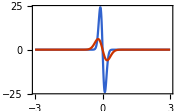

```mathematica
Block[{σs={0.1,0.2},sty=Style[#,FontFamily->"CMU"]&},
Plot[Evaluate@Table[-x Exp[-x^2/(2σ^2)]/(Sqrt[2π]σ^3),{σ,σs}],{x,-3,3},PlotRange->All,FrameLabel->{"\!\(x\)","\!\(δ\^′(x)\)"},PlotLegends->LineLegend[Automatic,sty/@σs,LegendLabel->sty@"\!\(σ=\)",LegendMargins->1],ImageSize->180]]
```

δ'(x_1-x_2) can be either understood as ∂_x_1 δ(x_1-x_2) or as -∂_x_2 δ(x_1-x_2). Under convolution,

∫ⅆ x_2δ'(x_1-x_2)ψ(x_2)
=∫ⅆx_2(-∂_x_2 δ(x_1-x_2))ψ(x_2)
=∫ⅆ x_2δ(x_1-x_2)(∂_x_2 ψ(x_2))
=∂_x_1 ψ(x_1),

so the kernel δ'(x_1-x_2) indeed implements differentiation under convolution.

In the matrix form,

∂_x ψ≏lim_(δx→0) 1/(2δx)(⋱ | ⋱ |   |   |  
⋱ | 0 | 1 |   |  
  | -1 | 0 | 1 |  
  |   | -1 | 0 | ⋱
  |   |   | ⋱ | ⋱)(⋮
ψ(x-δx)
ψ(x)
ψ(x+δx)
⋮)
=lim_(δx→0) (ψ(x+δx)-ψ(x-δx))/(2δx)≏∂_x ψ.

Note: to discretize δ'(x_1-x_2) without losing its essential meaning, we can consider

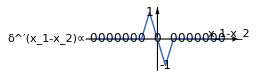

```mathematica
Block[{L=8,pts},
pts=Table[{x,If[Abs[x]==1,-x,0]},{x,-L,L}];
Graphics[{{Text["\!\(δ\^′(x\_1-x\_2)∝\)",{-L-1,0},{1,0}]},{AbsoluteThickness[0.8],Arrow[{0,#}&/@{-1.2,1.2}],Arrow[{#,0}&/@{-L-1,L+2}],Text["\!\(x\_1-x\_2\)",{L+1,0},{0,-1.2}]},{Blue,Line[pts]},Text[Style[Last@#,12],#]&/@pts},AspectRatio->0.3,ImageSize->260]]
```

Higher order derivatives: just multiply the matrix n times.

∂_x^n ≏δ^(n)(x_1-x_2)  or  lim_(δx→0) 1/(2δx)^n(⋱ | ⋱ |   |   |  
⋱ | 0 | 1 |   |  
  | -1 | 0 | 1 |  
  |   | -1 | 0 | ⋱
  |   |   | ⋱ | ⋱)^n.

The matrix representation of ∂_x  is not Hermitian! ⇒ ∂_x  is not a Hermitian operator, as

(∂_x)^†=∫ⅆ x_1ⅆ x_2x_1δ^(′*)(x_2-x_1)x_2
=-∫ⅆ x_1ⅆ x_2x_1δ'(x_1-x_2)x_2
=-∂_x .

We can make it Hermitian by giving it an imaginary factor -ⅈ ℏ, and define:

p̂=-ⅈ ℏ∂_x=-ⅈ ℏ∫ⅆ x_1ⅆ x_2x_1δ'(x_1-x_2)x_2.

Now p̂ is Hermitian, what physical observable does it correspond to? - It is the momentum operator. Why?

A hand-waving argument: the idea of path integral is that the phase Θ of the wave function ∼ the action S of the particle (by Θ=S/ℏ), i.e.

ψ∼e^(ⅈ Θ)∼e^(ⅈ S/ℏ),

therefore

p̂ ψ=-ⅈ ℏ∂_x e^(ⅈ S/ℏ)∼-ⅈ ℏ((ⅈ ∂_x S)/ℏ)e^(ⅈ S/ℏ)∼(∂_x S)ψ.

So the eigenvalues of p̂ would better correspond to ∂_x S, or more precisely, the variation of the action with respect to the final position, which is the momentum in classical mechanics (recall the result of HW Homework).

#### Position Operator

Position of the particle is also an physical observable. What Hermitian operator does it correspond to?

The position operator:

x̂=∫ⅆxxx x.

It is a diagonal operator (like a diagonal matrix) in the position basis ⇒ it just marks each position eigenstate x by the position eigenvalue x (which is the coordinate of the particle). It is a generalized example of the spectral decomposition of Hermitian operators L=∑_i λ_i λ_i λ_i.

The position operator x̂ acting on a state ψ=∫ⅆxxψ(x)

x̂ ψ=∫ⅆxⅆ x'xx xx'ψ(x')
=∫ⅆxⅆ x'xx δ(x-x')ψ(x')
=∫ⅆx (x ψ(x))x.

In terms of the wave function ψ(x), the position operator basically multiplies the wave function by the position x:

ψ(x)→^(x̂)x ψ(x).

A sloppy notation:

x̂ ψ(x)=x ψ(x).

The momentum operator p̂ acting on a state ψ=∫ⅆxxψ(x)

p̂ ψ=∫ⅆx x(-ⅈ ℏ∂_x ψ(x)).

Another sloppy notation:

p̂ ψ(x)=-ⅈ ℏ∂_x ψ(x).

#### Uncertainty Relation

So the position operator marks the wave function by x, the momentum operator mixes (changes) the wave function by derivatives. Markers and mixers do not commute!

[x̂,p̂]=ⅈ ℏ.

To see this, study how they act on a state

x̂ p̂ ψ(x)=-ⅈ ℏ x∂_x ψ(x),
p̂ x̂ ψ(x)=-ⅈ ℏ∂_x (x ψ(x))=-ⅈ ℏ ψ(x)-ⅈ ℏ x ∂_x ψ(x),

so the commutator

[x̂,p̂]ψ(x)=(x̂ p̂-p̂ x̂)ψ(x)
=-ⅈ ℏ x∂_x ψ(x)+ⅈ ℏ ψ(x)+ⅈ ℏ x ∂_x ψ(x)
=ⅈ ℏ ψ(x),

“eliminate” ψ(x) from both sides ⇒ [x̂,p̂]=ⅈ ℏ 𝟙.

Uncertainty Relation (between position and momentum): on any given state ψ of a particle, measure the position x and the momentum p (in separate experiments) repeatedly, the statistics of the measurement outcomes must obey

(std x)(std p)≥1/2|⟨[x̂,p̂]⟩|=ℏ/2.

If the particle has a precise position, i.e. (std x)→0, its momentum must fluctuate infinitely strong, i.e. (std p)→∞.

If we want to probe smaller and smaller structures of our space, we must use particles (say photons) with larger and larger momentum, until the energy E=c p of the photon becomes so large that the photon itself collapses into a black hole under its own gravity. ⇒ Quantum mechanics imposes a fundamental resolution limit of the space: the Planck length

ℓ_P=√((ℏ G)/c^3)≈1.616229(38)×10^-35 m.

Consider a state ψ=∫ⅆx ψ(x)x described by the following wave function with a tunable parameter σ: 
ψ(x)=1/(π^(1/4)σ^(1/2))exp(-x^2/(2 σ^2))
(i) Check that the state is normalized ψψ=1, regardless of the value of σ.
(ii) Evaluate the expectation values: ⟨x̂⟩, ⟨p̂⟩, ⟨(x̂)^2⟩, ⟨(p̂)^2⟩ in terms of σ.
(iii) Based on the result of (ii), calculate (std x) and (std p) in terms of σ. Do they satisfy the uncertainty relation?

### Dynamics and Symmetry

#### Hamiltonian and Time Evolution

Hamiltonian of a non-relativistic particle in classical mechanics

H=p^2/(2m)+V(x).

In quantum mechanics, just promote every physical observable to its operator,

Ĥ=(p̂)^2/(2m)+V(x̂)
=-ℏ^2/(2m)∂_x^2 +V(x̂).

By V(x̂) we mean

V(x̂)=∫ⅆxxV(x)x.

This is always how we define a function of an operator. Its action on a wave function ψ(x) (in the position basis) is simply to multiply it by V(x), sloppy notation:

V(x̂)ψ(x)=V(x)ψ(x).

The Schrödinger equation we derived previously in Eq. (DisplayFormulaNumbered) matches its general form of

ⅈ ℏ∂_t ψ=Ĥ ψ.

The Hamiltonian operator Ĥ is Hermitian. What physical observable does it correspond to? - Answer: the energy. Why?

A hand-waving argument: the idea of path integral is that the phase Θ of the wave function ∼ the action S of the particle (by Θ=S/ℏ), i.e.

ψ∼e^(ⅈ Θ)∼e^(ⅈ S/ℏ),

therefore

Ĥ ψ=ⅈ ℏ∂_t e^(ⅈ S/ℏ)∼ⅈ ℏ((ⅈ ∂_t S)/ℏ)e^(ⅈ S/ℏ)∼(-∂_t S)ψ.

So the eigenvalues of Ĥ would better correspond to -∂_t S, or more precisely, the (negative) variation of the action with respect to the final time, which is the energy in classical mechanics (recall the result of HW Homework).

Time evolution is unitary

ψ(t)=Û(t)ψ(0),

and it is generated by the Hamiltonian,

Û(t)=e^(-ⅈ Ĥ t /ℏ).

Then |ψ(t)⟩ can be further used to calculate the evolution of operator expectation values ...

In the Heisenberg picture, the state remains fixed while the operator evolves in time

L̂(t)=(Û(t))^†L̂ Û(t),

described by the Heisenberg equation

ⅈ ℏ∂_t L̂(t)=[L̂(t),Ĥ].

This will provide an equivalent description for the evolution of the operator expectation values.

Consider Ĥ=1/2(p̂)^2+1/2(x̂)^2, derive the Heisenberg equation for operator â=1/(√2)(x̂+ⅈ p̂).

#### Momentum and Space Translation

The momentum operator p̂, as a Hermitian operator, must also be able to generate a unitary operator. So what is the unitary operator generated by momentum? - Answer: it is the space translation operator

T̂(a)=e^(ⅈ p̂ a /ℏ).

Acting on a wave function ψ(x)

T̂(a)ψ(x)=e^(ⅈ p̂ a /ℏ)ψ(x)
=exp(a ∂_x)ψ(x)
=(𝟙+a ∂_x +a^2/(2!) ∂_x^2 +a^3/(3!)∂_x^3 +…)ψ(x)
=ψ(x)+a ψ'(x)+a^2/(2!) ψ''(x)+a^3/(3!)ψ^(3)(x)+…
=ψ(x+a).

So the unitary operator T̂(a) implements the space translation x→x+a, it is called the space translation operator.

Another equivalent definition of T̂(a) is

T̂(a)=∫ⅆxx-ax.

Such that given the state ψ=∫ⅆx ψ(x)x

T̂(a)ψ=∫ⅆxⅆ x'x-axx'ψ(x')
=∫ⅆxⅆ x'x-aδ(x-x')ψ(x')
=∫ⅆx ψ(x)x-a
=∫ⅆx ψ(x+a)x.

The inverse translation should be given by the Hermitian conjugate,

(T̂)^-1(a)=(T̂)^†(a)=∫ⅆxxx-a=∫ⅆxx+ax=T(-a).

Staring from the commutation relation [x̂,p̂]=ⅈ ℏ introduced in Eq. (DisplayFormulaNumbered).
(i) Show that [x̂,(p̂)^n]=ⅈ ℏ n (p̂)^(n-1) for all n∈ℕ by induction.
(ii) Use the above result to show that [x̂,F(p̂)]=ⅈ ℏ ∂_(p̂) F(p̂) for generic function F.
(ii) Apply the above result to the translation operator T̂(a) defined in Eq. (DisplayFormulaNumbered) to show that [x̂,T̂(a)]=-aT̂(a).
The final result implies that the position operator is indeed translated by the translation operator T̂(a)x̂(T̂)^†(a)=x̂+a 𝟙.

#### Symmetry and Conservation Laws

Applying the translation operator to:

the position operator x̂ → will shift the position

T̂(a)x̂(T̂)^†(a)
=∫ⅆ x_1x_1-ax_1∫ⅆ x_2x_2 x_2 x_2∫ⅆ x_3x_3x_3-a
=∫ⅆ x_1ⅆ x_2ⅆ x_3x_1-ax_1x_2 x_2 x_2x_3x_3-a
=∫ⅆ x_1x_1-a x_1 x_1-a
=∫ⅆxx(x+a)x
=∫ⅆxxxx+a∫ⅆxxx
=x̂+a 𝟙.

the momentum operator p̂ → will do nothing

T̂(a)p̂(T̂)^†(a)
=e^(ⅈ p̂ a /ℏ)p̂ e^(-ⅈ p̂ a /ℏ)
=e^(ⅈ p̂ a /ℏ)e^(-ⅈ p̂ a /ℏ)p̂
=p̂.

the Hamiltonian Ĥ → will only translate the potential profile

T̂(a)Ĥ(T̂)^†(a)
=T̂(a)((p̂)^2/(2m)+V(x̂))(T̂)^†(a)
=(p̂)^2/(2m)+V(x̂+a).

The Hamiltonian will be invariant under space translation, iff the potential is flat (position independent)

V(x+a)=V(x),

i.e. V(x)=const. In this case, we say the particle respects the space translation symmetry.

What is the significance of the space translation symmetry?

If T̂(a)Ĥ(T̂)^†(a)=Ĥ for any a, we can consider the limit a→0, then we must at least have

T̂(a)Ĥ(T̂)^†(a)=e^(ⅈ p̂ a /ℏ)Ĥ e^(-ⅈ p̂ a /ℏ)
=(𝟙+(ⅈ p̂ a)/ℏ+…)Ĥ(𝟙-(ⅈ p̂ a)/ℏ+...)
=Ĥ+(ⅈ a)/ℏ[p̂,Ĥ]+𝒪(a^2)=Ĥ,

meaning that to the first order in a, the commutator must vanish

[p̂,Ĥ]=0.

According to the Heisenberg equation of operator dynamics

ⅈ ℏ∂_t p̂(t)=[p̂(t),Ĥ]=0,

the momentum of the particle is conserved.

Noether’s theorem: every continuous (differentiable) symmetry of a physical system implies a corresponding conservation law.

Space translation symmetry ⇔ Momentum conservation

Time translation symmetry ⇔ Energy conservation

In quantum mechanics, symmetries are implemented by unitary operators, the corresponding Hermitian generators will describe the corresponding conserved physical observables.

What if the Hamiltonian is momentum independent? Does the momentum translation symmetry implies the position conservation? Yes!

Ĥ=(p̂)^2/(2m)+V(x̂)→^(m→∞)Ĥ=V(x̂).

The Hamiltonian becomes momentum independent in the limit of large particle mass. ⇒ In this limit, the position of the particle remains unchanged in time ⇒ Heavy particles are hard to move.

### Wave-Particle Duality

#### Momentum Basis

The momentum operator p̂ is a Hermitian operator in the single-particle Hilbert space. Eigenstates of the momentum operator should form a complete set of orthonormal basis as well ⇒ the momentum basis.

p̂ p=pp.

Eigenstates p are labeled by momentum eigenvalues p∈ℝ.

Any state in the single-particle Hilbert space can is a linear superposition of the momentum basis states,

ψ̃=∫ⅆp ψ̃(p)p.

Given the state ψ̃, the probability density to observe the particle with momentum p is

p(p)=(|pψ̃|)^2=(|ψ̃(p)|)^2.

We are free to choose basis: the position and momentum basis states can be written in terms of each other

p=1/(√(2π ℏ))∫ⅆx e^(ⅈ p x/ℏ)x,
x=1/(√(2π ℏ))∫ⅆp e^(-ⅈ p x/ℏ)p.

The normalization factor 1/√(2π ℏ) is just a matter of convention.

To verify the first equation in Eq. (DisplayFormulaNumbered)

p̂ p=1/(√(2π ℏ))∫ⅆx (-ⅈ ℏ∂_x e^(ⅈ p x/ℏ))x
=1/(√(2π ℏ))∫ⅆx (p e^(ⅈ p x/ℏ))x
=pp.

This implies

xp=1/(√(2π ℏ))e^(ⅈ p x/ℏ),
px=1/(√(2π ℏ))e^(-ⅈ p x/ℏ),

which leads to the second equation in Eq. (DisplayFormulaNumbered). The second equation further implies that

x̂=ⅈ ℏ ∂_p,
p̂=-ⅈ ℏ∂_x .

For a free particle, the Hamiltonian is a function of momentum only

Ĥ=(p̂)^2/(2m),

so the momentum eigenstates p are also energy eigenstates,

Ĥ p=p^2/(2m)p.

The position space wave function of momentum eigenstate is given by

xp=1/(√(2π ℏ))e^(ⅈ p x/ℏ),

also known as the plane wave solution of a free particle. However this wave function is not normalizable, indicating that the idea of free particle in a infinite space is not quite physical (in reality, particles are usually subject to some confining potential).

#### Fourier Transform

The fact that both position and momentum basis are complete ⇒ implies the following resolutions of identity, see Eq. (DisplayFormulaNumbered),

𝟙=∫ⅆxxx=∫ⅆppp.

Combining two identity operator ⇒ still an identity operator

𝟙=∫ⅆxⅆpxxpp=1/(√(2π ℏ))∫ⅆxⅆpx e^(ⅈ p x/ℏ)p,
𝟙=∫ⅆxⅆpppxx=1/(√(2π ℏ))∫ⅆxⅆpp e^(-ⅈ p x/ℏ)x.

They can be use to transform wave functions between position and momentum basis, e.g.

∫ⅆx ψ(x)x
=1/(√(2π ℏ))∫ⅆxⅆpp e^(-ⅈ p x/ℏ)x∫ⅆ x' ψ(x')x'
=1/(√(2π ℏ))∫ⅆxⅆpⅆ x'p e^(-ⅈ p x/ℏ)ψ(x')δ(x-x')
=1/(√(2π ℏ))∫ⅆxⅆpp e^(-ⅈ p x/ℏ)ψ(x)
=∫ⅆp ψ̃(p)p,

where ψ̃(p) is related to ψ(x) by Fourier transforms,

ψ̃(p)=1/(√(2π ℏ))∫ⅆx e^(-ⅈ p x/ℏ)ψ(x),
ψ(x)=1/(√(2π ℏ))∫ⅆp e^(ⅈ p x/ℏ)ψ̃(p).

In Eq. (DisplayFormulaNumbered), the same state is written in two different ways:

as a superposition of position basis ∫ⅆx ψ(x)x,

as a superposition of momentum basis ∫ⅆp ψ̃(p)p,

The superposition coefficients ψ(x) and ψ̃(p) will be related by Fourier transforms, for the two descriptions to be equivalent.

Sometimes we call ψ(x) the position (real) space wave function and ψ̃(p) the momentum space wave function.

This is an example of duality in physics: two seemly different descriptions actually correspond to the same physics.

The Fourier transform is also a special case of the more general representation transformation, which transforms between two arbitrary sets of basis.

### Quantum Planar Rotor

#### Rotor Basis

A planar rotor is a particle living on a ring:

```mathematica
DynamicModule[{x=0.3,dx=0.01,dyn=False},
Dynamic[If[dyn,x=Mod[x+dx,1]];EventHandler[Deploy[Row[{Graphics[{Line[{{0,0},{1,0}}],Translate[Line[Offset/@{{0,-2},{0,2}}],{#,0}]&/@{0,1},AbsolutePointSize[6],Point[{x,0}],Text["\!\(x\)",{x,0},{0,1.2}],Text["0",{0,0},{0,1.2}],Text["1",{1,0},{0,1.2}]},PlotRange->{{-0.2,1.2},{-1,1}},AspectRatio->0.5,ImageSize->100],Graphics[{Circle[{0,0},1],AbsolutePointSize[6],Point[ReIm@Exp[2π ⅈ x]],{AbsoluteThickness[0.8],{Dashed,Line[ReIm/@{0,Exp[2π ⅈ #]}]&/@{0,x}},Circle[{0,0},0.15,{0,2π x}],Text["θ",ReIm[0.3 Exp[π ⅈ x]]]},Text["0",{1.1,0},{-1,-0.5}],Text["2π",{1.1,0},{-1,0.5}]},PlotRange->1.5,ImageSize->100]},Alignment->Center]],{"MouseClicked":>(dyn=Not[dyn])}]]]
```

x∈[0,1) with periodic boundary condition, i.e. x=1 is equivalent to x=0.

Or in terms of angular variable θ=2π x, s.t. θ∈[0,2π) with θ=2π equivalent to θ=0.

The planar rotor Hilbert space can be spanned by a set of basis states θ labeled by the angle θ∈[0,2π), called the angular (position) basis or the rotor basis.

θ describes the state that the rotor is at a definite angular position θ.

All states θ form a orthonormal basis

θ_1θ_2=δ(θ_1-θ_2 mod 2π).

Any state of the planar rotor can be expanded as a linear superposition of the rotor basis states

ψ=∫_0^(2π) ⅆθ ψ(θ)θ.

Hereinafter, the integration of any angular variable θ is always assumed to be from 0 to 2π, as ∫_0^(2π) ⅆθ.

The periodicity of θ ⇒ θ and θ±2π are the same state (just different names). Any physical state/operator should be invariant under θ→θ±2π.

To avoid this naming redundancy, it is better to think that each θ actually labels an element e^(ⅈ θ) in the U(1) group, with the group multiplication rule

e^(ⅈ θ_1)e^(ⅈ θ_2)=e^(ⅈ (θ_1+θ_2)).

#### Rotation and Angular Momentum

Rotation operator: a unitary operator in the rotor Hilbert space that implements the rotation θ→θ+α.

R̂(α)=∫ⅆθθ-αθ.

As a unitary operator, the rotation operator R̂(α) also has a Hermitian generator N̂,

R̂(α)=e^(ⅈ N̂ α).

The operator N̂ can be found via

N̂=lim_(α→0) (-ⅈ ∂_α R̂(α))
=lim_(α→0) (-ⅈ ∂_α ∫ⅆθθ-αθ)
=lim_(α→0) (-ⅈ ∂_α ∫ⅆ θ_1ⅆ θ_2θ_1δ(θ_1-θ_2+α)θ_2)
=lim_(α→0) ∫ⅆ θ_1ⅆ θ_2θ_1(-ⅈ δ'(θ_1-θ_2+α))θ_2
=∫ⅆ θ_1ⅆ θ_2θ_1(-ⅈ δ'(θ_1-θ_2))θ_2

Acting N̂ on a state ψ=∫ⅆθ ψ(θ)θ,

N̂ ψ=∫ⅆθⅆ θ'θ(-ⅈ δ'(θ-θ'))ψ(θ')
=∫ⅆθⅆ θ'θ(-ⅈ δ(θ-θ')∂_θ' ψ(θ'))
=∫ⅆθ (-ⅈ ∂_θ ψ(θ))θ,

the effect is like (in sloppy notation)

N̂ ψ(θ)=-ⅈ ∂_θ ψ(θ).

Thus we identify the rotation generator N̂ to be

N̂=-ⅈ∂_θ=-ⅈ∫ⅆ θ_1ⅆ θ_2θ_1δ'(θ_1-θ_2)θ_2.

The rotation generator should be related to the angular momentum operator L̂. The precise relation is

L̂=N̂ ℏ,

as ℏ provides a natural unit for angular momentum (since they have the same dimension). If we set ℏ=1, we may also call N̂ as the (dimensionless) angular momentum operator of a planar rotor.

#### Angular Momentum Quantization

What are the eigenvalues and eigenstates of the angular momentum operator N̂? To figure out, we need to solve the eigen equation:

N̂ N=NN,

where the eigenstate N is label by the eigenvalue N, and can be written as a linear superposition of the rotor basis θ

N=∫ⅆθθθN,

with the wave function (the superposition coefficient) θN. Plugging Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) into Eq. (DisplayFormulaNumbered), we obtain

-ⅈ∂_θ θN=NθN⇒θN∝e^(ⅈ N θ).

After normalization

N=1/(√(2π))∫ⅆθ e^(ⅈ N θ)θ.

Verify that the state N in Eq. (DisplayFormulaNumbered) has been properly normalized, s.t. NN=1.

But recall the periodic boundary condition (or called the compactification condition): θ is equivalent to θ±2π ⇒ physical states must be invariant under θ→θ±2π ⇒ the eigenstate N is physical iff

N=R̂(2π)N
=e^(2π ⅈ N̂)N
=e^(2π ⅈ N)N,

which requires e^(2π ⅈ N)=1, i.e. the eigenvalue N must be an integer

N=0,±1,±2,…  or N∈ℤ.

If the coordinate is compact (like θ), the momentum will be quantized (like N).

The integer N is also called the angular momentum quantum number. As we restore the dimension, the angular momentum is quantized to N ℏ (in unit of ℏ).

The state N describes a quantum planar rotor with definite angular momentum N (or more precisely N ℏ).

N=0 state: a equal weight and equal phase superposition of all rotor basis

N=0=1/(√(2π))∫ⅆθ θ.

Zero angular momentum ⇒ the rotor is “static” (but not in the classical sense).

The probability to find the rotor at angle θ: p(θ)=1/(2π) ⇒ the rotor rests everywhere with equal probability ⇒ manifesting the uncertainty relation and quantum fluctuations.

N>0 states ⇒ positive angular momentum ⇒ counterclockwise rotating rotors.

N<0 states ⇒ negative angular momentum ⇒ clockwise rotating rotors.

#### Representation Transformation

As eigenstates of a Hermitian operator N̂, the states N also form a complete set of orthonormal basis for the rotor Hilbert space, called the angular momentum basis.

Unlike the rotor basis, the angular momentum basis is discrete. Its orthonormality implies

N_1N_2=δ_(N_1 N_2).

Its completeness implies

𝟙=∑_(N∈ℤ) NN.

The two sets of basis are related by

N=1/(√(2π))∫_(U(1)) ⅆθ e^(ⅈ N θ)θ,
θ=1/(√(2π))∑_(N∈ℤ) e^(-ⅈ N θ)N.

The basis transformations are implemented by Fourier transforms

𝟙=1/(√(2π))∑_(N∈ℤ) ∫_(U(1)) ⅆθ θ e^(ⅈ N θ)N,
𝟙=1/(√(2π))∑_(N∈ℤ) ∫_(U(1)) ⅆθ N e^(-ⅈ N θ)θ.

#### Free Planar Rotor

A free planar rotor is described by the following Hamiltonian

Ĥ=1/(2I)(L̂)^2=ℏ^2/(2I)(N̂)^2=-ℏ^2/(2I)∂_θ^2,

where I=m R^2 is the moment of inertia. Ĥ = the kinetic energy (operator) of the rotor. To make life easier, let us set ℏ^2 I^-1=1 (as our energy unit) and consider

Ĥ=1/2(N̂)^2.

The angular momentum eigenstates N are automatically energy eigenstates

Ĥ N=E_N N,
E_N=1/2 N^2.

The energy has a quadratic dependence on the quantum number N,

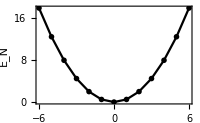

```mathematica
Block[{M=6},ListLinePlot[Table[{Ν,Ν^2/2},{Ν,-M,M}],PlotRangePadding->Scaled[0.03],GridLines->{Range[-M,M],Range[0,M]^2/2},PlotStyle->Black,PlotMarkers->Graphics[{EdgeForm[Black],White,Disk[{0,0},Offset[{2,2}]]}],
FrameLabel->{"\!\(N\)","\!\(E\_N\)"},ImageSize->200]]
```

The eigenenergies are discrete ⇒ energy levels.

The lowest energy eigenstate 0 is called the ground state. All the other higher energy eigenstates N (for N=±1,±2,…) are excited states.

The ground state of the free planar rotor is unique (non-degenerated). All the excited states are two-fold degenerated, i.e. level degeneracy = 2.

Density of state: number of states per energy interval (usually defined in the thermodynamic limit to smooth out the discreteness).

D(E)=ⅆN/ⅆE∝1/(√E).

If the rotor is electrically charged, it can be driven by electromagnetic field. It can absorb an incident photon of frequency ω and transits from the ground state 0 to an excited state N, if ℏ ω=E_N-E_0. The absorption rate (at low temperature) will be proportional to D(E_0+ℏ ω).

#### Reflection Symmetry

For N≠0, the two states N and -N are related by the reflection symmetry, under which θ→-θ and N→-N.

The symmetry can be implemented by the unitary operator P̂

P̂=∫ⅆθ-θθ=∑_N -NN.

It is a ℤ_2 symmetry, i.e. (P̂)^2=𝟙, so (P̂)^-1=(P̂)^†=P̂.

The Hamiltonian Ĥ is invariant under the symmetry transformation P̂

P̂ Ĥ P̂=Ĥ,

because Ĥ and P̂ commute.

(i) Use Eq. (DisplayFormulaNumbered) to show that ∫ⅆθ-θθ and ∑_N -NN are the same operator.
(ii) Show that Ĥ and P̂ commute, i.e. Ĥ P̂=P̂ Ĥ.

Using Eq. (DisplayFormulaNumbered), can show that

E_N N=Ĥ N=P̂ Ĥ P̂ N=P̂ Ĥ-N=E_-N P̂-N=E_-N N,

meaning that E_N=E_-N. So N and -N state must have the same energy (as long as N≠0) ⇒ hence the two-fold degeneracy of excited levels is enforced by symmetry.

More precisely, the degeneracy is protected jointly by the rotation and the reflection symmetry, denoted as the U(1)⋊ℤ_2 group. The group is defined by the following algebraic relations

R̂(α)R̂(β)=R̂(α+β),
(P̂)^2=𝟙,
R̂(α)P̂=P̂ R̂(-α).

The only one-dimensional irreducible representation is the trivial representation 0.

The rest of the irreducible representations are two-dimensional, as spanned by ±N for N=1,2,….

#### Raising and Lowering Operators

We have defined the angular momentum operator N̂ of the planar rotor. What about the angular position operator θ̂? - We may attempt to define:

θ̂=∫ⅆθθθθ.

However, it is ill-defined, because it is not invariant under the 2π-rotation.

R̂(2π)θ̂(R̂)^†(2π)=θ̂+2π 𝟙≠θ̂.

So the operator θ̂ is unphysical.

Then what operator(s) should we measure to determine the “position” of the rotor? - The raising and lowering operators,

e^(±ⅈ θ̂)=∫ⅆθθ e^(±ⅈ θ)θ.

e^(+ⅈ θ̂): raising operator, e^(-ⅈ θ̂) lowering operator.

Or to be Hermitian, what we really measure should be the real and imaginary parts of e^(±ⅈ θ̂)

cos θ̂=∫ⅆθθcos θθ,
sin θ̂=∫ⅆθθsin θθ.

Why are e^(±ⅈ θ̂) called raising and lowering?

e^(±ⅈ θ̂)N=e^(±ⅈ θ̂)1/(√(2π))∫ⅆθ e^(ⅈ N θ)θ
=1/(√(2π))∫ⅆθ e^(ⅈ N θ)e^(±ⅈ θ̂)θ
=1/(√(2π))∫ⅆθ e^(ⅈ N θ)e^(±ⅈ θ)θ
=1/(√(2π))∫ⅆθ e^(ⅈ (N±1) θ)θ
=N±1.

Because e^(±ⅈ θ̂) indeed raise or lower the angular momentum of the planar rotor.

e^(±ⅈ θ̂)=∑_N N±1N.

To compare:

θ̂ generates the shift of angular momentum e^(±ⅈ θ̂)=∑_N N±1N.

N̂ generates the rotation e^(ⅈ N̂ α)=∫ⅆθθ-αθ.

A free planar rotor, described by the Hamiltonian Ĥ=1/2(N̂)^2, was initial prepared in the state ψ(0)=(4π)^(-1/2)∫ⅆθ (1+e^(ⅈ θ))θ. Find the expectation value of the raising operator e^(ⅈ θ̂) as a function of time t. (May set ℏ=1 for simplicity.)

#### Charged Rotor in Electric Field

The electric field provides a potential energy for the charged particle

V(θ)=g (1-cos θ),

where g=q R|E| characterizes the strength of the electric field.

```mathematica
DynamicModule[{t=π/2,dt=0.12,dyn=False},
Dynamic[If[dyn,t=t+dt];
EventHandler[Deploy[Graphics[{Circle[{0,0},1],AbsolutePointSize[6],Point[ReIm@Exp[0.2π ⅈ Sin[t]]],{AbsoluteThickness[0.8],{Dashed,Line[ReIm/@{0,Exp[0.2π ⅈ Sin[t]]}]}},
{Arrowheads[0.1],AbsoluteThickness[1],Table[Arrow[{{-1.5,y},{1.5,y}}],{y,-1.2,1.2,0.6}],Text["\!\(E\)",{1.2,0.85}]}},PlotRange->1.5,ImageSize->100]],{"MouseClicked":>(dyn=Not[dyn])}]]]
```

The Hamiltonian operator

Ĥ=1/2(N̂)^2+g (𝟙-cos θ̂).

The potential term g can be written as raising/lowering operators

Ĥ=1/2(N̂)^2+g 𝟙-g/2 (e^(+ⅈ θ̂)+e^(-ⅈ θ̂))
=∑_N ((N^2/2+g)NN-g/2 N+1N-g/2 N-1N).

This provides a matrix representation of the Hamiltonian

Ĥ≏(⋱ | ⋱ |   |   |   |   |  
⋱ | 2+g | -g/2 |   |   |   |  
  | -g/2 | 1/2+g | -g/2 |   |   |  
  |   | -g/2 | g | -g/2 |   |  
  |   |   | -g/2 | 1/2+g | -g/2 |  
  |   |   |   | -g/2 | 2+g | ⋱
  |   |   |   |   | ⋱ | ⋱).

Eigenvalues and eigenstates of Ĥ can be obtained by diagonalizing the Hamiltonian (using the matrix form).

Ĥ n=E_n n.

Let us do it numerically:

In numerics, we need to truncate the angular momentum basis to N∈[-M,M], altogether 2M+1 basis states. If we only care about the low-energy physics, large angular momentum states are not important.

```mathematica
M=32;
```

We will consider a relatively large g, such that the rotor is almost pinned around θ=0 to do small oscillations ⇒ approximated by a harmonic oscillator.

```mathematica
g=256;
```

Ĥ→^(θ→0)1/2(N̂)^2+g/2 (θ̂)^2+….

Construct and diagonalize the Hamiltonian (a (2M+1)×(2M+1) matrix)

```mathematica
H=SparseArray[{Band[{1,1}]->Range[-M,M]^2/2+g,Band[{1,2}]->-g/2,Band[{2,1}]->-g/2},{2M+1,2M+1}];
eigs=SortBy[First]@Thread@Eigensystem@N@H;
```

Now eigs contains the full list of (E_n,n) pairs (that solves the eigen equation Eq. (DisplayFormulaNumbered)), with n represented by a state vector (ψ̃)_n in the angular momentum basis (each with 2M+1 components)

n=∑_N (ψ̃)_(n,N)N.

The low-lying energy levels (n≪M) follow a linear relation with the level index n ⇒ the neighboring level spacings are equal (denoted as ℏ ω)

E_n≃ℏ ω (n+1/2).

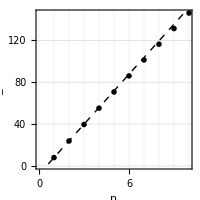

```mathematica
ListPlot[eigs⟦;;10,1⟧,GridLines->{Range[0,2M+1],Range[0,2M+1]eigs⟦1,1⟧},PlotStyle->Black,PlotMarkers->Graphics[{EdgeForm[Black],White,Disk[{0,0},Offset[{2,2}]]}],Prolog->{AbsoluteThickness[1],Dashed,Line[{#,eigs⟦1,1⟧(2(#-1)+1)}&/@{0,2M}]},
FrameLabel->{"\!\(n\)","\!\(E\_n\)"},AspectRatio->1,ImageSize->200]
```

In fact ω is related to g by ω=g^(1/2) (to be discussed later).

The density of state is uniform (E independent) at low-energy

D(E)=ⅆn/ⅆE≃1/(ℏ ω)=const.

Applying the electric field changes the low-energy density of state drastically. This is a measurable effect in the absorption spectrum D(E_0+ℏ ω).

What does the wave function of each eigenstate look like in the rotor basis?

n=∑_N (ψ̃)_(n,N)N
=1/(√(2π))∫ⅆθ ∑_N (ψ̃)_(n,N)e^(ⅈ N θ)θ
=∫ⅆθ ψ_n(θ)θ,

where ψ_n(θ) is given by

ψ_n(θ)=1/(√(2π))∑_N (ψ̃)_(n,N)e^(ⅈ N θ).

Some examples of the wave function ψ_n(θ) (blue - Re ψ_n(θ), red - Im ψ_n(θ)):

```mathematica
Row[Plot[Evaluate[ReIm[#3.Exp[ⅈ Range[-M,M]θ]]],{θ,-π,π},PlotRange->{-4.5,4.5},PlotLabel->Style["\!\(n="<>ToString[#1]<>"\)\n\!\(E\_"<>ToString[#1]<>"="<>ToString[NumberForm[#2/(2eigs⟦1,1⟧),3]]<>"ℏω\)",14],Frame->None,Ticks->{{-π,0,π},None},AxesLabel->{"θ",None},ImageSize->120]&@@@MapThread[Prepend,{#,Range[0,Length@#-1]}]&@eigs⟦;;6⟧]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

#### Potential Momentum

We have been talking about a quantum particle moving in a (energy) potential V(x),

Ĥ=(p̂)^2/(2m)+V(x̂).

Potential energy: as the particle moves from one position x_1 to another x_2, if V(x_1)≠V(x_2), the difference V(x_2)-V(x_1) will be released in the form of energy (and can be converted to the kinetic energy).

For a particle with charge q in an electrostatic potential φ(x), we have V(x)=q φ(x).

Is there also something like a potential momentum?

Potential momentum: as the particle travels from one time t_1 to another t_2, if q A(t_1)≠q A(t_2), the difference q A(t_2)-q A(t_1) will be released in the form of momentum (and can be converted to the kinetic momentum).

Is there any example of potential momentum?

Yes. A charged particle q on a ring with magnetic flux threading through the ring. Suppose we gradually turn on/off the magnetic field B, according to Faraday’s law of induction,

∫_Σ (∂B)/(∂t)·ⅆS=-∮_(∂Σ) E·ⅆl,

an induced electric field E will be generated to accelerate/decelerate the charge.

```mathematica
DynamicModule[{t=0,dt=0.05,v=0,a=0.1,state=0},
Dynamic[
Switch[state,
1,t=t+v dt;a=0.08;If[v<1,v=v+a dt,v=1];,
2,t=t+v dt;a=-0.08;If[v>0,v=v+a dt,v=0];,
0,Null];
EventHandler[Deploy[Graphics[{Circle[{0,0},1],AbsolutePointSize[6],Point[ReIm@Exp[-2π ⅈ t]],{AbsoluteThickness[0.8],{Dashed,Line[ReIm/@{0,Exp[-2π ⅈ t]}]}},
If[0<v<1,{Red,Arrowheads[0.1],AbsoluteThickness[1],Arrow[ReIm[# Exp[-Sign[a]ⅈ 2 π Range[0,64]/64]]&/@{0.7,1.2}],Text["\!\(E\)",{1.2,0.8}]},{}],
{Blue,Opacity[v],{Translate[{AbsoluteThickness[1],Circle[{0,0},0.1],AbsolutePointSize[3],Point[{0,0}]},#]&/@Cases[0.5Tuples[Range[-5,5],2].{{1/2,Sqrt[3]/2},{1/2,-Sqrt[3]/2}},p_/;Norm[p]<1],Text["\!\(B\)",{-0.28,-0.2}]}}},PlotRange->1.5,ImageSize->100]],{"MouseClicked":>(state=Mod[state+1,3])}]]]
```

The particle starts from rest. Just by threading the magnetic flux through the ring, the particle acquires (angular) momentum. ⇒ Magnetic field B generates a “potential momentum” q A for the surrounding charged particle

∫_Σ B·ⅆS=∮_(∂Σ) A·ⅆl ⟹^(on the ring)A=(B R)/2.

```mathematica
Graphics[{Circle[{0,0},1],AbsolutePointSize[6],
{AbsoluteThickness[0.8],Dashed,Line[ReIm/@{0,1}],Text["\!\(R\)",{0.45,0},{0,-0.7}]},
{Green,Arrowheads[0.1],AbsoluteThickness[1],Arrow[ReIm[# Exp[ⅈ 2 π Range[0,64]/64]]&/@{0.7,1.2}],Text["\!\(A\)",{1.2,0.8}]},
{Blue,{Translate[{AbsoluteThickness[1],Circle[{0,0},0.1],AbsolutePointSize[3],Point[{0,0}]},#]&/@Cases[0.5Tuples[Range[-5,5],2].{{1/2,Sqrt[3]/2},{1/2,-Sqrt[3]/2}},p_/;Norm[p]<1],Text["\!\(B\)",{-0.28,-0.2}]}}},PlotRange->1.5,ImageSize->100]
```

-Graphics-

Eq. (DisplayFormulaNumbered) and Eq. (DisplayFormulaNumbered) implies E=-∂_t A in this case
⇒ ∂_t (m v)=F=q E=-∂_t (q A)
⇒ ∂_t (m v+q A)=0,

m v - kinetic momentum,

q A - potential momentum,

total momentum (kinetic + potential)

p=m v+q A,

which is conserved.

How does the potential momentum enter the Hamiltonian?

The conserved energy/momentum are time/space translation generators. ⇒ They are directly related to the differential operators ∂_t  or ∂_x , including the contributions from both the kinetic and the potential parts.

{ | ⅈ ℏ∂_t=H=1/2 m v^2+q φ,
-ⅈ ℏ∂_x=p=m v+q A,⇒H=1/(2m)(p-q A)^2+q φ.

The Schrödinger equation of charged particle in electromagnetic field (in one-dimensional space)

ⅈ ℏ∂_t ψ=Ĥ ψ=[1/(2m)(-ⅈ ℏ ∂_x -q A)^2+q φ]ψ.

(A,φ) are also called the gauge potential. What do we mean by “gauge”? For simplicity, let us set ℏ=1 and q=1,

(ⅈ∂_t -φ)ψ=1/(2m)(-ⅈ ∂_x -A)^2 ψ.

Wave function ψ(x,t) is not physical, only the probability distribution p(x,t)=(|ψ(x,t)|)^2 is physical.

Attaching an arbitrary phase χ(x,t) to the wave function at each space time point

ψ(x,t)→e^(ⅈ χ(x,t))ψ(x,t)

does not affect p(x,t) ⇒ Eq. (DisplayFormulaNumbered) is a gauge transformation (= do-nothing/renaming)

However, gauge transformation does affect how ∂_t  and ∂_x  act on the wave function!

ⅈ ∂_t ψ→ⅈ∂_t (e^(ⅈ χ)ψ)=e^(ⅈ χ)(ⅈ∂_t -∂_t χ)ψ,
-ⅈ ∂_x ψ→-ⅈ ∂_x (e^(ⅈ χ)ψ)=e^(ⅈ χ)(-ⅈ∂_x +∂_x χ)ψ.

φ and A must transform accordingly to keep the Schrödinger equation Eq. (DisplayFormulaNumbered) invariant

φ→φ-∂_t χ,
A→A+∂_x χ,
ψ→e^(ⅈ χ)ψ.

The equations in Eq. (DisplayFormulaNumbered) is the full set of gauge transformations for both the gauge potentials (gauge field) and the wave function of charged particles (matter field).

*In higher dimensional space-time, using the relativistic notation A^μ=(φ,A)

ψ→e^(ⅈ χ)ψ, A_μ→A_μ+∂_μ χ.

The local phase redundancy of quantum wave function ⇔ the gauge redundancy of the potential A_μ (under gauge transformation the electromagnetic field strength F_(μ ν)=∂_μ A_ν-∂_ν A_μ remains unchanged).

#### Charged Rotor in Magnetic Field

If the charged particle is confined on a ring (as a planar rotor), with magnetic flux Φ through the ring, the Hamiltonian will be

Ĥ=ℏ^2/(2I)(N̂-N_Φ)^2,

where N_Φ=Φ/Φ_0 and Φ_0=h/q is the magnetic flux quantum.

```mathematica
Graphics[{Circle[{0,0},1],AbsolutePointSize[6],
{AbsoluteThickness[0.8],Dashed,Line[ReIm/@{0,1}],Text["\!\(R\)",{0.45,0},{0,-0.7}]},
{Green,Arrowheads[0.1],AbsoluteThickness[1],Arrow[ReIm[# Exp[ⅈ 2 π Range[0,64]/64]]&/@{0.7,1.2}],Text["\!\(A\)",{1.2,0.8}]},
{Blue,{Translate[{AbsoluteThickness[1],Circle[{0,0},0.1],AbsolutePointSize[3],Point[{0,0}]},#]&/@Cases[0.5Tuples[Range[-5,5],2].{{1/2,Sqrt[3]/2},{1/2,-Sqrt[3]/2}},p_/;Norm[p]<1],Text["\!\(B\)",{-0.28,-0.2}]}}},PlotRange->1.5,ImageSize->100]
```

-Graphics-

Magnetic flux Φ=∫_Σ B·ⅆS=∮_(∂Σ) A·ⅆl,

Φ=π R^2 B=2π R A.

Linear potential momentum q A

q A=(q Φ)/(2π R).

Angular potential momentum L_Φ=R×(q A)

L_Φ=R (q A)=(q Φ)/(2π).

in unit of ℏ (recall that L=ℏ N)

N_Φ=L_Φ/ℏ=(q Φ)/(2π ℏ)=Φ/(h/q)=Φ/Φ_0.

Physical meaning of N_Φ: number of magnetic flux in unit of the flux quantum. Note: the flux quantum depends on the charge carrier q: electrons in a metallic nano-ring q=e, Cooper pairs in a superconducting ring (SQUID) q=2e.

Again, let us set ℏ^2 I^-1=1, and consider

Ĥ=1/2(N̂-N_Φ 𝟙)^2.

Obviously, angular momentum eigenstates N are still energy eigenstates, but the energy spectrum is shifted by N_Φ (tunable by magnetic flux Φ)

Ĥ N=E_N N,
E_N=1/2(N-N_Φ)^2.

If Φ is fine tuned to Φ=Φ_0/2, i.e. N_Φ=1/2,

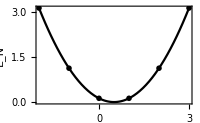

```mathematica
Block[{},
Show[Plot[(Ν-1/2)^2/2,{Ν,-2,3},PlotStyle->Black],
ListPlot[Table[{Ν,(Ν-1/2)^2/2},{Ν,-2,3}],PlotStyle->Black,PlotMarkers->Graphics[{EdgeForm[Black],White,Disk[{0,0},Offset[{2,2}]]}]],
GridLines->{Range[-2,3],(Range[3]-1/2)^2/2},
FrameLabel->{"\!\(N\)","\!\(E\_N\)"},ImageSize->200]]
```

The two-fold degenerated ground states N=0 and N=1 can be treated as a qubit, if the excitation gap is sufficiently large.

#### Quantum Anomaly*

What is the symmetry protecting the two-fold degeneracies in the N_Φ=1/2 quantum rotor model?

Ĥ=1/2(N̂-𝟙/2)^2.

An anomalous reflection symmetry that takes N→1-N,

P̂'=∑_N 1-NN=e^(+ⅈ θ̂)∑_N -NN=e^(+ⅈ θ̂)P̂,

where

P̂=∑_N -NN was the conventional reflection operator in Eq. (DisplayFormulaNumbered).

The anomalous reflection P̂' is the conventional reflection P̂ followed by the rasing operator e^(+ⅈ θ̂), which can be considered as a gauge transformation by redefining each rotor basis state by a different phase factor

θ→e^(ⅈ θ̂)θ=e^(ⅈ θ)θ.

The rotation and anomalous reflection symmetries together protect the degeneracy.

R̂(α)R̂(β)=R̂(α+β),
(P̂)^(′2)=𝟙,
R̂(α)P̂'=e^(ⅈ α)P̂' R̂(-α).

Compared to Eq. (DisplayFormulaNumbered), the symmetry representation in Eq. (DisplayFormulaNumbered) is said to be anomalous because of the additional phase factor e^(ⅈ α) (as a gauge transformation). The gauge transformation e^(ⅈ α) has no classical analogy, and is purely a quantum effect.

Is there any other physical consequence of the anomalous symmetry action?

If we break the rotation symmetry from continuous rotation (U(1) group) to two-fold discrete rotation (ℤ_2 group).

Ĥ=1/2(N̂-N_Φ 𝟙)^2-g_2 cos 2 θ̂-g_4 cos 4 θ̂-g_6 cos 6 θ̂-…

Classical level: the system respects two symmetries

Two-fold rotation R(π): θ→θ+π,

Reflection P: θ→-θ.

Quantum level: the symmetry group depends on N_Φ

N_Φ=0 | N_Φ=1/2
(R̂(π))^2=𝟙,
(P̂)^2=𝟙,
R̂(π)P̂=P̂ R̂(π) | (R̂(π))^2=𝟙,
(P̂)^(′2)=𝟙,
R̂(π)P̂'=-P̂'R̂(π)
ℤ_2×ℤ_2 | ℤ_2⋊ℤ_2

ℤ_2×ℤ_2 is Abelian and admits one-dimensional representations ⇒ allows non-degenerated levels to appear in the spectrum

ℤ_2⋊ℤ_2 does not admit one-dimensional representations (its representation is two-dimensional) ⇒ all energy levels are two-fold degenerated

Take the following potential V(θ) that preserves two-fold rotation and reflection symmetries.

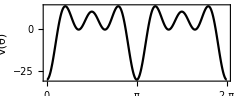

```mathematica
Block[{g=10},Plot[-g Cos[2θ]-g Cos[4θ]-g Cos[6θ],{θ,0,2π},PlotStyle->Black,Axes->False,FrameTicks->{Automatic,{{0,{π/2,"π/2"},π,{3π/2,"3π/2"},2π},Automatic}},FrameLabel->{"θ","\!\(V(θ)\)"},AspectRatio->0.4,ImageSize->240]]
```

The spectra for N_Φ=0,1/2 are

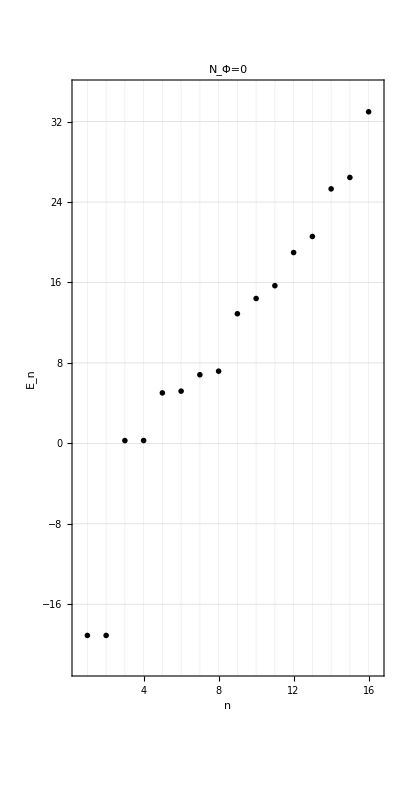
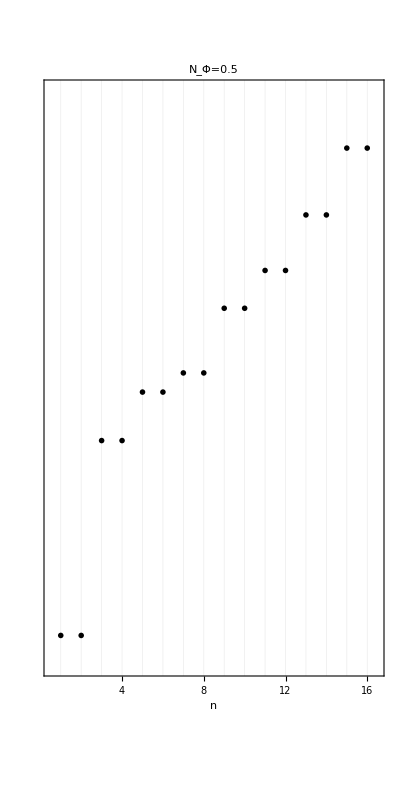

```mathematica
Row@Table[Block[{M=32,g=10,H,Es},
H=SparseArray[{Band[{1,1}]->(Range[-M,M]-NΦ)^2/2,Band[{1,3}]->-g/2,Band[{3,1}]->-g/2,Band[{1,5}]->-g/2,Band[{5,1}]->-g/2,Band[{1,7}]->-g/2,Band[{7,1}]->-g/2},{2M+1,2M+1}];
Es=Sort@Eigenvalues[N@H];
ListPlot[Es⟦;;16⟧,PlotRange->{{0.5,16.5},{-22,35}},
GridLines->{Range[0,2M+1],Es},PlotStyle->Black,PlotMarkers->Graphics[{EdgeForm[Black],White,Disk[{0,0},Offset[{2,2}]]}],PlotLabel->StringTemplate["\!\(N\_Φ=`1`\)"][NΦ],FrameLabel->{"\!\(n\)",If[NΦ==0,"\!\(E\_n\)",None]},Axes->False,FrameTicks->{If[NΦ==0,{Automatic,Automatic},{None,Automatic}],{Automatic,Automatic}},AspectRatio->2,ImageSize->{Automatic,260}]],{NΦ,{0,1/2}}]
```

At N_Φ=1/2, the quantum anomaly leads to exact degeneracies at all levels.

In fact, similar Hamiltonian is used to realize the superconducting qubit for quantum computation,

H=1/2(E_C(N̂-N_e 𝟙))^2-E_J cos 2 θ̂,

although the physical meaning of N̂ and cos θ̂ are interpreted differently:

N̂: the number of electrons in the capacitor,

cos 2 θ̂: the operator describing Cooper pair tunneling through a Josephson junction.

It is so far the most popular qubit architecture, under active development by Google, Microsoft, IBM, Rigetti, and Intel.